## Basics

Weird error: don’t use the variable name “Ground”, since that is a function
Also don’t use “I”, “E”, “N” since those are built-in things (unless you define them as local variables in a Module[]...)

## Functions

## General

#### Debug

Two useful functions for when you’re debugging another function, or to easily make a function print/echo things if you tell it to

```mathematica
PrintDebug[debug_,x___]:=If[debug,Print[x]];
```

```mathematica
EchoDebug[debug_,x___]:=If[debug,Echo[x],x];
```

```mathematica
PrintDebug[False,"a"]
```

```mathematica
EchoDebug[True,"Thing","Label"]
```

Label Thing

Thing

```mathematica
debug=True;
Do[PrintDebug[debug,i],{i,1,3}]
```

1

2

3

The function defined below has an optional “debug” parameter that defaults to False. Set it to True if you want the extra outputs.

```mathematica
example1[a_,b_,c_,debug_:False]:=Module[{},
PrintDebug[debug,"Now it's gonna echo some things"];
EchoDebug[debug,a^2,"a^2"];
EchoDebug[debug,b^2,"b^2"];
a+b+c
]
```

```mathematica
example1[3,2,1,True]
```

Now it's gonna echo some things

a^2 9

b^2 4

6

Here’s a fancy version showing the basics of options patterns (like how in Plot[] you can set Range→whatever)
I don’t usually use this, but if you ever have complicated code that can have tons of optional inputs but usually just takes default values, this might be a good idea

```mathematica
example2[a_,b_,c_,OptionsPattern[{DebugMode->False}]]:=Module[{debug},
debug=OptionValue[DebugMode];
PrintDebug[debug,"Now it's gonna echo some things"];
EchoDebug[debug,a^2,"a^2"];
EchoDebug[debug,b^2,"b^2"];
a+b+c
]
```

```mathematica
example2[3,2,1,DebugMode->True]
```

Now it's gonna echo some things

a^2 9

b^2 4

6

#### TimeToString

Helps when giving time estimates
It’s also cool if you have the program send you an SMS when it finishes running, with the total time in the message

Time given in seconds

```mathematica
TimeToString[t_]:=Which[
StringQ[t],
t,
t<60,
ToString[Round[t,0.01]]~~" seconds",
t<3600,
ToString[Round[t/60,0.01]]~~" minutes",
True,
ToString[Round[t/3600,0.01]]~~" hours"
]
```

```mathematica
t=12345;
SendMessage["SMS","Code finished running, took "~~TimeToString[t]~~"."]
```

## Matroids

I represent matroids in terms of bases, ie. as the tuple {E,B} where E is the ground set (as a list) and B is a list of bases (ie. B ⊆ 2^E)

### Matroid Construction

#### UniformMatroid

Constructs the uniform matroid U_(d,n)

```mathematica
UniformMatroid[d_,n_Integer]:={Range[n],Subsets[Range[n],{d}]}
```

```mathematica
UniformMatroid[2,4]
```

{{1,2,3,4},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}

For a non-standard ground set

```mathematica
UniformMatroid[d_,ground_List]:={ground,Subsets[ground,{d}]}
```

```mathematica
UniformMatroid[2,Subsets[Range[4],{2}]]
```

{{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},{{{1,2},{1,3}},{{1,2},{1,4}},{{1,2},{2,3}},{{1,2},{2,4}},{{1,2},{3,4}},{{1,3},{1,4}},{{1,3},{2,3}},{{1,3},{2,4}},{{1,3},{3,4}},{{1,4},{2,3}},{{1,4},{2,4}},{{1,4},{3,4}},{{2,3},{2,4}},{{2,3},{3,4}},{{2,4},{3,4}}}}

#### GraphicMatroid

Constructs the graphic matroid corresponding to a graph (or a set of edges)
Optional parameter “echo” if the user wants to see the graph

```mathematica
GraphicMatroid[G_,echo_:False]:=Module[{edges,numberingRule,B},

(*Finds the edges; requires figuring out if a graph or edge list was supplied*)
edges=If[GraphQ@G,EdgeList@G,G];

(*Numbers them automatically*)
numberingRule=Table[edges[[i]]->i,{i,1,Length@edges}];

(*Outputs the graph (if desired)*)
If[echo,Echo[Graph[edges,EdgeLabels->numberingRule],"Graph"]];

(*Determines the minimum spanning trees, which are the bases of our matroid*)
B=EdgeList/@Select[
Graph/@Subsets[edges,{EdgeCount@FindSpanningTree@G}]
,AcyclicGraphQ
]/.numberingRule;

{Range[Length@edges],B}
];
```

#### DualMatroid

Constructs the dual matroid

```mathematica
DualMatroid[M_]:=Module[{E,B},
{E,B}=M;
{E,Sort[Complement[E,#]&/@B]}
]
```

```mathematica
DualMatroid[UniformMatroid[2,5]]
```

{{1,2,3,4,5},{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}}

#### MK4

A good graphic matroid.
Giansiracusa^2 (A Grassman Algebra for Matroids) uses this one for examples (see examples 4.3.2, 6.1.5), so I decided to save it for easy use.
It’s useful since it’s a small nonuniform matroid.

```mathematica
MK4=GraphicMatroid[{1<->2,2<->4,4<->1,1<->3,3<->2,3<->4}];
```

#### LinearMatroid

Constructs a matroid from a matrix

```mathematica
LinearMatroid[A_]:=Module[{d,C,E,B},
(*Find the rank of the matroid*)
d=MatrixRank[A];
(*So that the rows are the vectors I care about*)
C=Transpose[A];
(*Find the ground set*)
E=Range[Length[C]];

(*Find bases*)
B=Table[If[MatrixRank[C[[indices]]]==d,indices,Nothing],{indices,Subsets[E,{d}]}];

(*Output*)
{E,B}
]
```

```mathematica
A={{-1,1,1,8,2,6,4},{-1,3,2,22,10,15,14},{0,1,1,10,4,9,5},{-1,1,2,14,2,15,4},{0,1,-1,-2,4,-9,5}};
MatrixForm[A]
M=LinearMatroid[A]
```

(-1 | 1 | 1 | 8 | 2 | 6 | 4
-1 | 3 | 2 | 22 | 10 | 15 | 14
0 | 1 | 1 | 10 | 4 | 9 | 5
-1 | 1 | 2 | 14 | 2 | 15 | 4
0 | 1 | -1 | -2 | 4 | -9 | 5)

{{1,2,3,4,5,6,7},{{1,2,3},{1,2,4},{1,2,6},{1,3,4},{1,3,5},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,6,7},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,7},{2,5,6},{2,6,7},{3,4,6},{3,4,7},{3,5,6},{3,5,7},{3,6,7},{4,5,6},{4,5,7},{4,6,7},{5,6,7}}}

```mathematica
rules=(#/.{List->Rule})&/@Transpose[{Range[7],{a,b,c,d,e,f,g}}]
```

{1→a,2→b,3→c,4→d,5→e,6→f,7→g}

```mathematica
Circuits[M]/.rules
```

{{a,b,e},{a,b,g},{a,c,f},{a,e,g},{b,d,f},{b,e,g},{c,d,e},{a,b,c,d},{a,c,d,g},{a,d,e,f},{a,d,f,g},{b,c,d,g},{b,c,e,f},{b,c,f,g},{c,d,f,g},{c,e,f,g},{d,e,f,g}}

### Matroid Parts

#### IndependentSets

```mathematica
IndependentSets[M_]:=With[{B=Last[M]},Union@@(Subsets[#]&/@B)]
```

```mathematica
IndependentSets[UniformMatroid[2,5]]
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

#### DependentSets

```mathematica
DependentSets[M_]:=With[{E=First[M]},Complement[Subsets[E],IndependentSets[M]]]
```

```mathematica
DependentSets[UniformMatroid[2,5]]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

#### Circuits

Using the swanky minimality-checking code I found online
Is there another way? Matroid of rank d, say we consider sets A of size d+1. Then the complements of bases in A give elements of a circuit in A.

```mathematica
Circuits[M_]:=Minimal[DependentSets[M]]
```

```mathematica
Circuits[UniformMatroid[2,5]]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

#### Cocircuits

Finds the cocircuits of a matroid

```mathematica
Cocircuits[M_]:=Circuits[DualMatroid[M]]
```

#### Rank

Gives the rank of a matroid

```mathematica
Rank[M_]:=Length[M[[2,1]]]
```

```mathematica
Rank[UniformMatroid[3,6]]
```

3

Gives the rank of a set in a matroid

```mathematica
Rank[S_,M_]:=Module[{bases},
(*Rank[S] is the size of the largest portion of S overlapping with a basis*)
bases=Last[M];
Max[Table[Length@Intersection[S,basis],{basis,bases}]]
]
```

```mathematica
Rank[{1,2,3,4},UniformMatroid[3,6]]
```

3

#### Closure

Computes the closure (flat) of a set S in a matroid M, using Lemma 3.2
Can instead supply the circuits of M in place of M

```mathematica
Closure[S_,M_]:=Module[{circuits,additionalElements,circuitExcess},

(*If M represents a matroid, take its circuits; otherwise, assume M is the circuits*)
(*Ex. M={{1,2,3},{{1,2},{1,3},{2,3}}} - note how the depth of E is the depth of B minus 1, so I can tell this is a matroid*)
circuits=If[Length@M==2∧Differences[Depth/@M]=={1},Circuits[M],M];

(*for each circuit, finds if it indicates an element to add to the closure of S*)
additionalElements=Table[
circuitExcess=Complement[circuit,S];
If[Length@circuitExcess==1,First@circuitExcess,Nothing]
,{circuit,circuits}];

(*add the indicated elements onto S to form its closure*)
Union[S,additionalElements]

]
```

#### Flats

Gives the flats of a matroid
The Subsets[E] step is computationally terrible; there should be some theorem which reduces how many subsets need to be used to find all the flats
	ie. Maybe when the size of S is bigger than the rank of M, the closure of S is E? Or similar.
Or, could compute flats as intersections of hyperplanes

```mathematica
Flats[M_]:=Module[{E,circuits,subsets,flats},
E=First[M];
circuits=Circuits[M];

subsets=Subsets[E];

flats=Table[
If[Closure[S,circuits]==S,S,Nothing]
,{S,subsets}];
Sort@flats
]
```

#### FlatsCongruences

Finds the congruence classes of subsets of E
The representatives of the classes are the flats of the matroid
Very similar to Flats[] above

```mathematica
FlatsCongruences[M_]:=Module[{E,circuits,subsets,closures},
E=First[M];
circuits=Circuits[M];

(*Since all subsets of size ≥Rank[M] have closure E, only need to bother computing closures for some of the subsets*)
subsets=Subsets[E];
closures=Table[
S->Closure[S,circuits]
,{S,subsets}];

(*"Invert" the association, so flats map to their congruence classes*)
GroupBy[closures,Last->First]

]
```

```mathematica
FlatsCongruences[UniformMatroid[2,4]]
```

<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{1,2,3,4}→{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}|>

#### Hyperplanes

Finds the hyperplanes of a matroid, as the complements of cocircuits.

```mathematica
Hyperplanes[M_]:=With[{E=First@M},Table[Complement[E,K],{K,Cocircuits[M]}]]
```

```mathematica
Hyperplanes[UniformMatroid[3,6]]
```

{{5,6},{4,6},{4,5},{3,6},{3,5},{3,4},{2,6},{2,5},{2,4},{2,3},{1,6},{1,5},{1,4},{1,3},{1,2}}

#### Ground

Gives the ground set of a matroid

```mathematica
Ground[M_]:=First[M]
```

### Misc

#### Minimal

Given a list of sets, finds the minimal sets by inclusion
Code taken from Mathematica Stack Exchange

```mathematica
Minimal[sets_]:=Module[{f,g,op=SystemOptions["DefinitionsReordering"]},
g[f[x__]]:=(f[x,___]=1;{x});
g[1]=Sequence[];
SetAttributes[f,Orderless];
SetSystemOptions["DefinitionsReordering"->"None"];
#&[
g[f@@#]&/@Sort@sets,
SetSystemOptions[op]
]

]
```

```mathematica
Minimal[{{1,2,3},{4,5,6},{2,1}}]
```

{{1,2},{4,5,6}}

#### LatticeOfFlats

Displays the lattice of flats of a matroid

```mathematica
LatticeOfFlats[M_]:=Module[{congruences,flats,levels},
congruences=FlatsCongruences[M];
flats=Sort@Keys[congruences];

(*Each level of the Hasse diagram corresponds to flats of a certain rank*)
levels=GatherBy[flats,Rank[#,M]&];

Print@DisplayLattice[levels];

congruences
]
```

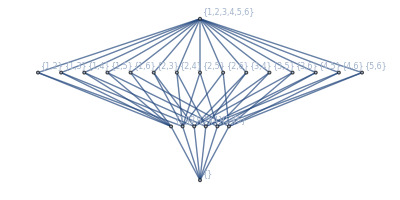

<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{5}→{{5}},{6}→{{6}},{1,2}→{{1,2}},{1,3}→{{1,3}},{1,4}→{{1,4}},{1,5}→{{1,5}},{1,6}→{{1,6}},{2,3}→{{2,3}},{2,4}→{{2,4}},{2,5}→{{2,5}},{2,6}→{{2,6}},{3,4}→{{3,4}},{3,5}→{{3,5}},{3,6}→{{3,6}},{4,5}→{{4,5}},{4,6}→{{4,6}},{5,6}→{{5,6}},{1,2,3,4,5,6}→{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6},{1,2,5,6},{1,3,4,5},{1,3,4,6},{1,3,5,6},{1,4,5,6},{2,3,4,5},{2,3,4,6},{2,3,5,6},{2,4,5,6},{3,4,5,6},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6},{1,2,3,4,5,6}}|>

```mathematica
LatticeOfFlats[UniformMatroid[3,6]]
```

#### C3Q

Determines whether a collection of sets satisfies the C3 axiom for circuits

(Note: from here on, C1, C2, and C3 will refer to sets)

Considers all pairs of circuits C1 and C2
	Is there a more efficient way?

```mathematica
C3Q[circuits_]:=Module[{C1,C2,union,possibleC3},
Catch[(*Catches the result of the function, ie whether circuits satisfies the C3 axiom*)

Do[(*Loops over possible C1 and C2 sets*)

(*Preliminaries*)
C1=circuits[[i]];
C2=circuits[[j]];
union=Union[C1,C2];
(*The only possibilities for the C3 circuit are those contained in C1 ∪ C2*)
possibleC3=Select[circuits,SubsetQ[union,#]&];

(*Check if for each x∈(C1 ∩ C2) there is an element of possibleC3 that does not contain x; ie. a valid choice for the C3 circuit*)
Do[

Catch[(*Allows for early termination of looking for said C3*)

(*Check each possible C3; we are interested in when C3 does not contain x*)
Do[
If[Not@MemberQ[C3,x],Throw[True,"x"](*Valid C3 found for this x*)]
,{C3,possibleC3}];

(*If you made it here, no valid C3 was found for this x, return False*)
Throw[False,
Echo["Failed, for"];
Echo[C1];
Echo[C2];
Echo[x];
"r"];

,"x"];
(*If you made it here, a valid C3 was found for this x*)

,{x,Intersection[C1,C2]}];
(*If you made it here, a valid C3 was found for all x's*)

,{i,1,Length@circuits},{j,i+1,Length@circuits}];
(*If you made it here, a valid C3 was found for all x's over all C1 and C2*)

(*Return True as the value of the function*)
True

,"r"]
]
```

#### B3Q

Determines whether a collection of sets satisfies the B3 axiom for bases

(Note: from here on, B1, B2, and B3 will refer to sets)
B3 is what we hope/expect the B1-x+y set to be

Considers all pairs of bases B1 and B2
	Is there a more efficient way?

```mathematica
B3Q[bases_]:=Module[{B1,B2,B3,B1sansB2,swaps,X,x,y},
Catch[(*Catches the result of the function, ie whether circuits satisfies the C3 axiom*)

Do[(*Loops over possible B1 and B2 sets*)

(*Preliminaries*)
If[i==j,Continue[]];
B1=bases[[i]];
B2=bases[[j]];
B1sansB2=Complement[B1,B2];

(*Keeps track of which x∈(B1-B2) weve found successful swaps for*)
swaps=AssociationThread[B1sansB2,False];

(*Loop over all the bases, seeing if we find a swap for each x∈(B1-B2)*)
(*If at any point we realize this is not a valid x, y swap, Continue[] the loop*)
Do[
(*First, check if B3 can be obtained from B1 with a single swap*)
(*X are the elements dropped*)
(*x is the single element dropped*)
X=Complement[B1,B3];
If[Length[X]≠1,Continue[]];
x=X[[1]];

(*If we already verified a swap for this x, keep looping*)
If[swaps[x]==True,Continue[]];

(*If the element we have to drop is in B2, it is not an x∈(B1-B2)*)
If[MemberQ[B2,x],Continue[]];

(*Find the y we have to add so that B3 = B1-x+y*)
y=Complement[B3,B1][[1]];

(*Check this y is valid, ie. y∈(B2-B1)*)
If[x≠y∧MemberQ[B2,y],
(*It is valid, so we document it*)
swaps[x]=True;
];

,{B3,bases}];

(*If any of the possible x didnt have swaps, we have failed*)
If[Not[And@@swaps],
Echo["Failed, for"];
x=Position[swaps,False][[1,1,1]];
Echo[B1];
Echo[B2];
Echo[x];
Throw[False];
];

,{i,1,Length[bases]},{j,1,Length[bases]}];

(*If you got here, there were valid swaps for all x for all B1 and B2*)
True
]
]
```

```mathematica
M=UniformMatroid[3,6];
B=M[[2]]
B3Q[B]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6}}

True

```mathematica
M=UniformMatroid[3,6];
B=M[[2,1;;-3]]
B3Q[B]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6}}

Failed, for

{1,5,6}

{3,4,5}

1

False

#### FQ

Checks the flat axioms

```mathematica
FQ[E_,Flats_]:=Module[{n,F1,F2,containers,coverers,partition,counts},
Catch[
(*F1*)
If[Not@MemberQ[Flats,E],
Echo["Failed F1"];
Throw[False]
];

(*F2*)
Do[
If[Not@MemberQ[Flats,Intersection@@pair],
Echo["Failed F2 for"];
Echo[pair[[1]],"F_1"];
Echo[pair[[2]],"F_2"];
Throw[False]
]
,
{pair,Subsets[Flats,{2}]}
];

(*F3*)
(*Maybe revise this to do some fancy Orderless thing like in Minimal[]*)
n=Length[E];
Do[
containers=Select[Flats,SubsetQ[#,F]&];
coverers=Minimal[Complement[containers,{F}]];
partition=Complement[#,F]&/@coverers;
counts=Tally[Join@@partition][[All,2]];
If[Length[counts]+Length[F]≠n,
Echo["Failed F3 for"];
Echo[F,"F"];
Echo["Union of F_i-F is not E-F"];
Throw[False]
];
If[Not@AllTrue[counts,#==1&],
Echo["Failed F3 for"];
Echo[F,"F"];
Echo["F_i-F have overlaps"];
Throw[False]
]
,
{F,Flats}
];

Throw[True]
]
]
```

```mathematica
classes=WedgeCongruences[UniformMatroid[3,4],2];
```

Trivial and bend 0.

Remaining set 0.183268

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.0000799

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.5668788

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

```mathematica
groundN=Subsets[Range[4],{2}];
FQ[groundN,Keys[classes]]
```

True

#### MatroidFromCircuits

Given a ground set E and a set of circuits, construct the matroid (in terms of bases).

Is there another more efficient way to code this?
Right now, it does
1. Find all possible subsets
2. Filter out the dependent sets (ie the ones that contain circuits)
3. Find the bases

Alternative idea: maybe leverage the fact that all circuits are basic (additionally, in each of their elements) - see Gordon McNulty p. 162 Proposition 4.7 part 1

```mathematica
MatroidFromCircuits[E_,C_]:=Module[{ind,d},
(*Trivial case*)
If[C=={},Return[{E,{E}}]];

(*Find independent sets*)
ind=Table[If[AnyTrue[C,SubsetQ[subset,#]&],Nothing,subset],{subset,Subsets[E]}];

(*Bases and return*)
d=Max@@(Length/@ind);
{E,Select[ind,Length[#]==d&]}
]
```

#### DisplayLattice

Given a list of the ascending levels of a lattice, display the lattice. It figures out the relations between elements on its own.

```mathematica
DisplayLattice[levels_]:=Module[{coords,edges},

(*Determines coordinates for vertices representing flats*)
coords=Module[{xSpacings,ySpacing,width,avg},
(*Finds the max number of characters in the name of a flat in each level*)
(*Then divides to get the horizontal spacing for that level*)
xSpacings=Table[Max[(StringLength@ToString@#)&/@level]/4,{level,levels}];

(*Accounting for horizontal spacings, finds the max width of a level*)
(*Then divides to get the vertical spacing between levels*)
ySpacing=Max[MapThread[(Length[#1]-1)*#2&,{levels,xSpacings}],1]/6;

coords=
Table[
(*These represent the width and average x-value of the level in terms of number of elements*)
(*ie. need to be scaled by xSpacings*)
width=Length[levels[[y]]];
avg=(width+1)/2;
Table[
(*This will make sure the digram is centered and the rows are well-spaced*)
{xSpacings[[y]](x-avg),ySpacing(y)}
,{x,width}]
,{y,Length[levels]}];

Flatten[coords,1]
];

(*Determines which flats are linked in the Hasse diagram*)
(*I'm assuming the only links will be between adjacent levels, I hope that's right*)
edges=Module[{level1,level2,parents},
edges=
Table[
level1=levels[[y]];
level2=levels[[y+1]];

(*For each flat in a level, find the edges that will go to the next level in the Hasse diagram*)
Table[
(*Find the flats that contain it*)
parents=Select[level2,SubsetQ[#,flat]&];
(*Turn this into graph edges*)
Table[flat<->parent,{parent,parents}]
,{flat,level1}]

,{y,Length[levels]-1}];

Flatten[edges,3]
];

(*The Hasse diagram*)
Graph[Flatten[levels,1],edges,VertexCoordinates->coords,VertexLabels->Automatic,VertexLabelStyle->8]
]
```

#### MatrixWedge

Given a matrix with full row rank, the span of its rows represents a linear space. Take a wedge power of this linear space by wedging rows together.
There’s actually a Mathematica function perfect for this, but I’ll still have this method as a wrapper.

```mathematica
MatrixWedge[A_,k_]:=Minors[A,k]
```

## Tropical

These I haven’t used in a while, so there’s a chance they’re shitty.
I think I originally used them when I was figuring out the correspondence between Plücker vectors and matroids, so they may be largely obsolete

### Basics

#### PluckerQ

Checks if a vector is a Plücker vector. The vector is represented by a matroid.

```mathematica
PluckerQ[M_]:=Module[{E,B,d,summation},
{E,B}=M;
d=Length[B[[1]]];
Catch[
Do[
summation=Table[
MemberQ[B,DeleteCases[A,i]]∧MemberQ[B,Union[B,{i}]]
,{i,Complement[A,B]}];
If[Count[summation,True]==1,Throw[False]]
,{A,Subsets[E,d+1]},{B,Subsets[E,d-1]}];
Throw[True]
]
]
```

### L_M

#### TropicalHyperplane

Calculates the tropical hyperplane corresponding to a Plücker vector
ie tropker(–⋀[M])
I think my code does it for the simple case over the boolean idempotent semifield, since I don’t take into account coefficients.

```mathematica
TropicalHyperplane[M_]:=Module[{E,B,forms,in,out},
E=First[M];

(*get the linear forms, Union[] to avoid redundant ones, Complement[] to remove the trivial one*)
forms=Complement[Union@LinearForms[M],{}];

Intersection@@Table[Tropker[E,form],{form,forms}]

]
```

#### LinearForms

Finds the linear forms corresponding to a Plücker vector (using the |J| = d+1 thing)
“Output” corresponds to whether it should echo the J that give trivial linear forms

```mathematica
LinearForms[M_,Output_:False]:=Module[{E,B,d,temp,forms},
{E,B}=M;
d=Length[B[[1]]];

(*find the linear form for each J*)
forms=Table[
temp=Table[If[MemberQ[B,DeleteCases[J,i]],i,Nothing],{i,J}];
If[Output∧Length@temp==0,Echo@J];
temp
,{J,Subsets[E,{d+1}]}];

(*remove duplicates and the trivial*)
Complement[Union[forms],{{}}]

]
```

#### Tropker

Finds the tropical kernel of a linear form

```mathematica
Tropker[E_,form_]:=Module[{in,out},

(*read what happens in the Union[], then these should make more sense*)
in=Subsets[form,{2,Length@form}];
out=Subsets[Complement[E,form]];

Union[
out,(*=0 case: pick from things not in the form*)
(Union@@#)&/@Tuples[{in,out}](*=1 case: pick at least two things in the form*)
]

]
```

#### OrthogonalDual

Given a list of linear forms, find their orthogonal dual as defined in GG2017 p.11

```mathematica
OrthogonalDual[E_,forms_]:=Module[{clean},
clean=Complement[forms,{{}}];
If[Length[clean]==0,
Subsets[E],
Intersection@@Table[Tropker[E,form],{form,clean}]
]
]
```

#### DoubleOrthogonalDual

Does the above function twice

```mathematica
DoubleOrthogonalDual[E_,forms_]:=OrthogonalDual[E,OrthogonalDual[E,forms]]
```

### Q_M

#### QuotientModule

Generates Q_M corresponding to a Plücker vector
ie B(–⋀[M])
Uses that ℒ(M)≅Q_M, G+2 Thm. 3.3
Currently, outputs it as an association of F→{S_i} associating flats to the sets in their equivalence class

Used to be called TropicalCongruences[]

```mathematica
TropicalCongruences[M_]:=Module[{E,subsets,flats,closures},
E=First[M];
subsets=Subsets[E];
flats=Flats[M];

(*computes closures, as the smallest flat containing it; the list "flats" is assumed to be sorted*)
(*this is an association, S -> cl(S) *)
closures=Association@Table[
S->Catch[Do[If[SubsetQ[flat,S],Throw[flat]],{flat,flats}]]
,{S,subsets}];

(*inverts the association, associating possible closures F to the sets S with cl(S) = F *)
PositionIndex@closures

]
```

```mathematica
TropicalCongruences[UniformMatroid[3,6]]
```

<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{5}→{{5}},{6}→{{6}},{1,2}→{{1,2}},{1,3}→{{1,3}},{1,4}→{{1,4}},{1,5}→{{1,5}},{1,6}→{{1,6}},{2,3}→{{2,3}},{2,4}→{{2,4}},{2,5}→{{2,5}},{2,6}→{{2,6}},{3,4}→{{3,4}},{3,5}→{{3,5}},{3,6}→{{3,6}},{4,5}→{{4,5}},{4,6}→{{4,6}},{5,6}→{{5,6}},{1,2,3,4,5,6}→{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6},{1,2,5,6},{1,3,4,5},{1,3,4,6},{1,3,5,6},{1,4,5,6},{2,3,4,5},{2,3,4,6},{2,3,5,6},{2,4,5,6},{3,4,5,6},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6},{1,2,3,4,5,6}}|>

## Congruences

### Main

#### MatroidalQ

Checks if a pair (M,k) is matroidal, by computing congruence classes (with WedgeCongruences[] and BendCongruences[]) and then checking the flat axioms with FQ[]

```mathematica
MatroidalQ[M_,k_]:=Module[{groundM,groundN,reps},
(*Give an estimate for the time needed*)
(*To edit this estimate, change the function MatoridalQTimeEstimate*)
(*Echo[TimeToString@MatroidalQTimeEstimate[M,k],"ETA"];*)

(*Do the thing*)
groundM=First[M];
groundN=Subsets[groundM,{k}];

reps=Keys@WedgeCongruences[M,k,False];

FQ[groundN,reps]
]
```

#### MatroidalQTimeEstimate

```mathematica
MatroidalQTimeEstimate[M_,k_]:="FIXME lol"
```

#### BendCongruences

Generates the congruences corresponding to a set of linear forms, and a ground set E. ie. ℬ(x_1+x_2+x_3) kind of stuff.
Each form should be given as a list, ie. x_1+x_2+x_3={1,2,3}. This matches how I represent things like circuits, which can also be viewed as linear forms.

Note that this can produce the same results as QuotientModule[], but QuotientModule[] uses the isomorphism to the lattice of flats to greatly simplify things.
This function is for more general settings where a matroidal interpretation may not exist, such as ⋀^k Q_M kinds of things.

Setting the 3rd parameter to False suppresses outputs, and only returns the congruences classes as a list (no graph of the congruences is printed).

How it works: - FIXME

```mathematica
BendCongruences[E_,forms_,debug_:True]:=Module[{subsets,l,reps,getRoot,support,noChangeCount,totalPairs,s1,s2,leaf,target,root,t0,t,looping={},i=0,lastChangeIndex,lastChangePair,changes,return,lengths,maxs,mins,data},

t0=AbsoluteTime[];

(*Useful variables*)
subsets=Subsets[E];
l=2^Length[E];

(*Set trivial representatives*)
reps=Association@Table[s->s,{s,subsets}];

(*Define a function to simplify things*)
getRoot[s_]:=FixedPoint[reps,s];

(*Set bend congruences representatives*)
Do[
leaf=Drop[form,{i}];
If[reps[leaf]==leaf,
reps[leaf]=form,
root=getRoot[leaf];
target=getRoot[form];
reps[root]=reps[target]=Union[root,target]
],

{form,forms},{i,1,Length[form]}
];

If[debug,
t=AbsoluteTime[];
Echo[t-t0,"Trivial and bend"];
Print[];
];

(*Generate new congruences*)
noChangeCount=0;
totalPairs=Binomial[l,2];
Catch[
While[True,
changes=0;
Do[
i++;
(*The sets involved*)
s1=subsets[[i1]];
s2=subsets[[i2]];
root=getRoot[Union[s1,s2]];
target=getRoot[Union[getRoot[s1],getRoot[s2]]];

(*Merge trees if necessary*)
If[root==target,
noChangeCount++,
(*EchoDebug[debug,{s1,s2,root,target}];*)
changes++;
lastChangeIndex=i;
lastChangePair={i1,i2};
noChangeCount=0;
reps[root]=reps[target]=Union[root,target];
];

If[noChangeCount==totalPairs,Throw[0]],

{i1,l},{i2,i1+1,l}
];
looping=Append[looping,changes];
];
];
looping=Append[looping,changes];

If[debug,
Print[];
t0=t;
t=AbsoluteTime[];
Echo[t-t0,"Remaining set"];
Echo[Length[E],"Ground set size"];
Echo[l,"Number of subsets"];
Echo[totalPairs,"Number of pairs"];
Echo[i,"Iterations needed"];
Echo[N[(t-t0)/i,3],"Avg time per iteration"];
Echo[N[i/totalPairs],"Loops done"];
Echo[looping,"Changes done each loop"];
Echo[lastChangeIndex,"Last change index"];
Echo[subsets[[lastChangePair]],"Last change pair"];
Print[];
];

(*Collapse trees into direct links to representatives*)
Do[
reps[s]=reps[reps[s]],
{s,Reverse[subsets]}
];

If[debug,
t0=t;
t=AbsoluteTime[];
Echo[t-t0,"Tree collapsed"];
Print[];
];

(*Visualize*)
(*PrintDebug[debug,Graph[Normal[reps],VertexLabels->Automatic]];*)

(*Reverse-lookup the association*)
return=reps//Normal//GroupBy[Last->First]//Sort;

(*Print basic info*)
If[debug,
lengths=Length/@Values[return];
maxs=Length/@Keys[return];
mins=Min[Length/@#]&/@Values[return];
data=Transpose@{lengths,maxs,mins};
data=GatherBy[data,First];
data=Table[{stats[[1,1]],Length[stats],Max[stats[[All,2]]],Min[stats[[All,3]]]},{stats,data}];

Print@TableForm[Prepend[data,{"Class size","#","Max elem. size","Min elem. size"}]];
Print["Longest linear form length: ",Max[Length/@forms]];
];

return

]
```

#### WedgeCongruences

Applies bend congruences for a wedge power of a matroid

```mathematica
WedgeCongruences[M_,k_,output_:True]:=Module[{Cpre,wedgeE},
(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];
(*The linear forms*)
Cpre=PreExpectedCircuits[M,k];
BendCongruences[wedgeE,Cpre,output]
]
```

#### WedgeLattice

Similar to WedgeCongruences, but also displays a lattice
If Cwedge satisfies C3, orders the lattice by rank
	Otherwise, does it by length

```mathematica
WedgeLattice[M_,k_,output_:True]:=Module[{Cexp,wedgeE,components,representatives,CexpDD,Cwedge,Mwedge,f,levels},

(*First, the WedgeCongruences section*)
(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];
(*The expected circuits, ie. linear forms*)
Cexp=ExpectedCircuits[M,k];
(*Note that "components" is an association*)
components=BendCongruences[wedgeE,Cexp,output];

(*Pick the representatives*)
representatives=Sort@Keys@components;
(*Next, group these representatives into levels*)
(*If Cwedge satisfies C3, sort into levels by rank; otherwise, sort into levels by length*)
CexpDD=DoubleOrthogonalDual[wedgeE,Cexp];
Cwedge=Minimal[Complement[CexpDD,{{}}]];
If[C3Q[Cwedge],
Mwedge=MatroidFromCircuits[wedgeE,Cwedge];
f=Rank[#,Mwedge]&,
f=Length
];
levels=GatherBy[representatives,f];

Print@DisplayLattice[levels];

components
]
```

28 Set initial congruences from bend relations and self-congruences

226 Closed as a submodule, needs closing as an equivalence relation

226 Closed as both a submodule and equivalence relation

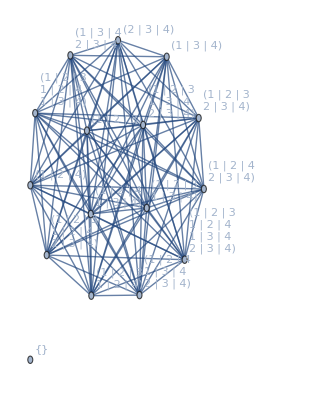

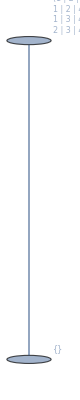

<|{}→{{}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}→{{{1,2,3},{1,2,4}},{{1,2,3}},{{1,2,4}},{{1,3,4}},{{2,3,4}},{{1,2,3},{1,3,4}},{{1,2,3},{2,3,4}},{{1,2,4},{1,3,4}},{{1,2,4},{2,3,4}},{{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4}},{{1,2,3},{1,2,4},{2,3,4}},{{1,2,3},{1,3,4},{2,3,4}},{{1,2,4},{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}}|>

```mathematica
WedgeLattice[UniformMatroid[3,4],3]
```

#### VisualizeCongruences

Prints the graph visualizing a set of congruences

```mathematica
VisualizeCongruences[classes_]:=Module[{reps,E,edges},
reps=Keys[classes];
E=Last[reps];
edges=Table[
child->rep,{rep,reps},
{child,Complement[classes[rep],{rep}]}
];
edges=Flatten[edges,1];
Graph[Subsets[E],edges,VertexLabels->Automatic]
]
```

```mathematica
classes=WedgeCongruences[UniformMatroid[3,4],2];
```

Trivial and bend 0.

Remaining set 0.158284

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.000069

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.5912458

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

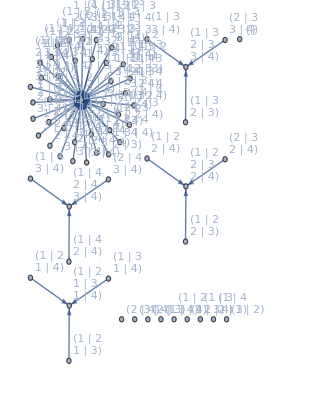

```mathematica
VisualizeCongruences[classes]
```

### New

#### MatroidalQNew

Checks if a pair (M,k) is matroidal, by computing congruence classes (with WedgeCongruences[] and BendCongruences[]) and then checking the flat axioms with FQ[]

```mathematica
MatroidalQNew[M_,k_]:=Module[{groundM,groundN,reps},
(*Give an estimate for the time needed*)
(*To edit this estimate, change the function MatoridalQTimeEstimate*)
(*Echo[TimeToString@MatroidalQTimeEstimate[M,k],"ETA"];*)

(*Do the thing*)
groundM=First[M];
groundN=Subsets[groundM,{k}];

reps=Keys@WedgeCongruencesNew[M,k,False];

FQ[groundN,reps]
]
```

#### BendCongruencesNew

Generates the congruences corresponding to a set of linear forms, and a ground set E. ie. ℬ(x_1+x_2+x_3) kind of stuff.
Each form should be given as a list, ie. x_1+x_2+x_3={1,2,3}. This matches how I represent things like circuits, which can also be viewed as linear forms.

Note that this can produce the same results as QuotientModule[], but QuotientModule[] uses the isomorphism to the lattice of flats to greatly simplify things.
This function is for more general settings where a matroidal interpretation may not exist, such as ⋀^k Q_M kinds of things.

Setting the 3rd parameter to False suppresses outputs, and only returns the congruences classes as a list (no graph of the congruences is printed).

How it works: - FIXME

```mathematica
BendCongruencesNew[E_,forms_,debug_:True]:=Module[{subsets,l,reps,getRoot,support,s1,s2,leaf,target,root,t0,t,i,lastChangeIndex,lastChangePair,return,lengths,maxs,mins,data},

t0=AbsoluteTime[];

(*Useful variables*)
subsets=Subsets[E];
l=Length[E];

(*Set trivial representatives*)
reps=Association@Table[s->s,{s,subsets}];

(*Define a function to simplify things*)
getRoot[s_]:=FixedPoint[reps,s];

(*Set bend congruences representatives*)
Do[
leaf=Drop[form,{i}];
If[reps[leaf]==leaf,
reps[leaf]=form,
root=getRoot[leaf];
target=getRoot[form];
reps[root]=reps[target]=Union[root,target]
],

{form,forms},{i,1,Length[form]}
];

If[debug,
t=AbsoluteTime[];
Echo[t-t0,"Trivial and bend"];
Print[];
];

(*Generate new congruences*)
i=0;
Catch[
Do[
(*The sets involved*)
s1=subsets[[i1]];
s2=subsets[[i2]];
root=getRoot[Union[s1,s2]];
target=getRoot[Union[getRoot[s1],getRoot[s2]]];

(*Merge trees if necessary*)
If[root==target,,
i++;
lastChangePair={i1,i2};
reps[root]=reps[target]=Union[root,target];
],

{i1,1,1+l},{i2,i1+1,2^l}
];
];

If[debug,
Print[];
t0=t;
t=AbsoluteTime[];
Echo[t-t0,"Remaining set"];
Echo[Length[E],"Ground set size"];
Echo[(2^l-1)+l(2^l-l-1),"Number of pairs checked"];
Echo[i,"Changes done"];
Echo[lastChangePair,"Last change indices"];
Echo[subsets[[lastChangePair]],"Last change pair"];
Echo[N[((2^l-1)+l(2^l-l-1))/(t-t0),3],"Avg iterations per second"];
Print[];
];

(*Collapse trees into direct links to representatives*)
Do[
reps[s]=reps[reps[s]],
{s,Reverse[subsets]}
];

If[debug,
t0=t;
t=AbsoluteTime[];
Echo[t-t0,"Tree collapsed"];
Print[];
];

(*Visualize*)
(*PrintDebug[debug,Graph[Normal[reps],VertexLabels->Automatic]];*)

(*Reverse-lookup the association*)
return=reps//Normal//GroupBy[Last->First]//Sort;

(*Print basic info*)
If[debug,
lengths=Length/@Values[return];
maxs=Length/@Keys[return];
mins=Min[Length/@#]&/@Values[return];
data=Transpose@{lengths,maxs,mins};
data=GatherBy[data,First];
data=Table[{stats[[1,1]],Length[stats],Max[stats[[All,2]]],Min[stats[[All,3]]]},{stats,data}];

Print@TableForm[Prepend[data,{"Class size","#","Max elem. size","Min elem. size"}]];
Print["Longest linear form length: ",Max[Length/@forms]];
];

return

]
```

#### WedgeCongruencesNew

Applies bend congruences for a wedge power of a matroid

```mathematica
WedgeCongruencesNew[M_,k_,output_:True]:=Module[{Cpre,wedgeE},
(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];
(*The linear forms*)
Cpre=PreExpectedCircuits[M,k];
BendCongruencesNew[wedgeE,Cpre,output]
]
```

#### WedgeLatticeNew

Similar to WedgeCongruences, but also displays a lattice
If Cwedge satisfies C3, orders the lattice by rank
	Otherwise, does it by length

```mathematica
WedgeLatticeNew[M_,k_,output_:True]:=Module[{Cexp,wedgeE,components,representatives,CexpDD,Cwedge,Mwedge,f,levels},

(*First, the WedgeCongruences section*)
(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];
(*The expected circuits, ie. linear forms*)
Cexp=ExpectedCircuits[M,k];
(*Note that "components" is an association*)
components=BendCongruencesNew[wedgeE,Cexp,output];

(*Pick the representatives*)
representatives=Sort@Keys@components;
(*Next, group these representatives into levels*)
(*If Cwedge satisfies C3, sort into levels by rank; otherwise, sort into levels by length*)
CexpDD=DoubleOrthogonalDual[wedgeE,Cexp];
Cwedge=Minimal[Complement[CexpDD,{{}}]];
If[C3Q[Cwedge],
Mwedge=MatroidFromCircuits[wedgeE,Cwedge];
f=Rank[#,Mwedge]&,
f=Length
];
levels=GatherBy[representatives,f];

Print@DisplayLattice[levels];

components
]
```

```mathematica
WedgeLattice[UniformMatroid[3,4],3]
```

28 Set initial congruences from bend relations and self-congruences

226 Closed as a submodule, needs closing as an equivalence relation

226 Closed as both a submodule and equivalence relation

-Graphics-

-Graphics-

<|{}→{{}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}→{{{1,2,3},{1,2,4}},{{1,2,3}},{{1,2,4}},{{1,3,4}},{{2,3,4}},{{1,2,3},{1,3,4}},{{1,2,3},{2,3,4}},{{1,2,4},{1,3,4}},{{1,2,4},{2,3,4}},{{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4}},{{1,2,3},{1,2,4},{2,3,4}},{{1,2,3},{1,3,4},{2,3,4}},{{1,2,4},{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}}|>

## Expected Circuits

### Construction

#### PreExpectedCircuits

The first set I generate, of just wedging circuits with additional elements

```mathematica
PreExpectedCircuits[M_,k_]:=Module[{subsets,circuits,nonzero,return},
subsets=Subsets[First[M],{k-1}];
circuits=Circuits[M];

return=Table[
Union[I,{elem}]
,{circuit,circuits},{I,subsets},{elem,Complement[circuit,I]}];

Union@Flatten[return,1]

]
```

#### ExpectedCircuits

The minimal elements of the pre expected circuits

```mathematica
ExpectedCircuits[M_,k_]:=Minimal[Complement[PreExpectedCircuits[M,k],{{}}]]
```

#### WedgeCircuits???

Not optimized
Probably runs in terrible time, since there are likely steps to skip or something
Idea: maybe I can use Cpre instead of Cexp when going into the double orthogonal dual

```mathematica
WedgeCircuits[M_,k_]:=Minimal[Complement[DoubleOrthogonalDual[Subsets[Ground[M],{k}],ExpectedCircuits[M,k]],{{}}]]
```

### Misc

#### CircuitCompletion???

Given some collection Cexp (or more generally, any collection of subsets of a ground set that satisfy C1 and C2 axioms), adds additional elements such that

```mathematica
CircuitCompletion[Cexp_]:=Module[{},

]
```

### Congruences Proof

No longer needed, since I finished the proof (using these functions to help understand the various cases)

#### CoverQ

Checks if the sets in SubCollection “cover” the sets in Collection; ie if every element of Collection can be expressed as a union of elements of SubCollection

```mathematica
CoverQ[SubCollection_,Collection_]:=Module[{collection,subsets},

(*remove the trivial cases of a union of a single element*)
collection=Complement[Collection,SubCollection];

Catch[

(*check the covering condition for each element in the collection*)
Do[
(*if it isn't covered, Echo[] the counterexample and exit*)
(*regular == should be fine since I everything is ordered correctly, ie. won't be comparing {1,2} to {2,1} and getting False*)
If[Not[Union@@Select[SubCollection,SubsetQ[set,#]&]==set],Echo[set,"Fails for"];Throw[False]]
,{set,collection}];

Throw[True]
]

]
```

#### ExpectedCircuitsCoverQ

Like CoverQ but takes the matroid and k, and first generates the pre expected circuits and expected circuits, and see if they cover.
Saves the step of regenerating C_pre to find C_exp.

```mathematica
ExpectedCircuitsCoverQ[M_,k_]:=Module[{pre,exp},
pre=PreExpectedCircuits[M,k];
exp=Minimal[Select[pre,#≠{}&]];
CoverQ[exp,pre]
]
```

## Useful

## Matroids

How to import the data from http://www-imai.is.s.u-tokyo.ac.jp/~ymatsu/matroid/ to our format
Must format their data as a .txt file that looks like:

#### Data file format

Some text in the beginning where I can describe
what’s in this file
etc. etc.

START

2 1
**
0*

3 1
***
0**
00*

n d
Matroid codes

#### Get matroids

Pick data file

```mathematica
f=SystemDialogInput["FileOpen"];
```

Load and interpret data

```mathematica
(*Read in file*)
matroidCodes=ReadList[f,String];

(*Remove everything before START*)
i=Position[matroidCodes,"START"][[1,1]];
matroidCodes=Drop[matroidCodes,i];

(*Split at the n,d*)
codesList=SplitBy[matroidCodes,StringContainsQ[#,"*"]&];

(*Interpret the codes, and form an association "matroids"*)
(*Elements are {n,d}->{list of matroids with those n,d}*)
matroids=Association@Table[
{n,d}=ToExpression@StringSplit[codesList[[2i-1,1]]];
rawCodes=codesList[[2i]];

groundSet=Range[n];
subsets=Reverse@Subsets[groundSet,{d}];

codedBases=ToCharacterCode@rawCodes;
l=Length[First[codedBases]];
decodedBases=Reverse/@Table[If[bases[[i]]==42,subsets[[i]],Nothing],{bases,codedBases},{i,1,l}];
Ms=Transpose@{Table[groundSet,Length[decodedBases]],decodedBases};

{n,d}->Ms

,{i,1,Length[codesList]/2}];
```

Check B3 axiom
May take a while, don’t need to do this if you trust the data file and code

```mathematica
Ms=Flatten[Values[matroids],1];
B3Q[Last[#]]&/@Ms;
```

#### Save matroids

```mathematica
f=SystemDialogInput["FileSave"];
Export[f,matroids]
```

C:\Users\Nick\Documents\Undergrad\Labs\Marcus\Data\matroids.txt

#### Load matroids

```mathematica
f=SystemDialogInput["FileOpen"];
matroids=ToExpression@Import[f]
```

#### Alternative format

If you don’t really care about the {n,d} of the matroids, you can do the following to just obtain a list of the matroids

```mathematica
matroidsList=Flatten[Values[matroids],1]
```

## Work

## 2/25

### Testing new BendCongruences[]

#### 1

```mathematica
M=UniformMatroid[3,4];
k=2;
```

```mathematica
{t,new}=Timing@WedgeCongruences[M,k];
t
```

Trivial and bend 0.

Remaining set 0.0977362

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.0000426

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.449799

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

0.046875

#### 2

```mathematica
M=UniformMatroid[3,5];
k=2;
```

```mathematica
{t,new}=Timing@WedgeCongruences[M,k];
t
```

Trivial and bend 0.001995

Remaining set 10.024441

Ground set size 10

Number of subsets 1024

Number of pairs 523776

Iterations needed 534009

Avg time per iteration 0.0000188

Loops done 1.01954

Changes done each loop {932,0}

Last change index 10233

Last change pair {{{4,5}},{{1,2},{1,3},{2,3}}}

Tree collapsed 0.4134774

Class size | # | Max elem. size | Min elem. size
1 | 26 | 2 | 0
11 | 5 | 4 | 2
943 | 1 | 10 | 3

Longest linear form length: 4

9.95313

#### 3

```mathematica
M=UniformMatroid[4,5];
k=2;
```

```mathematica
{t,new}=Timing@WedgeCongruences[M,k];
t
```

Trivial and bend 0.002033

Remaining set 9.9423067

Ground set size 10

Number of subsets 1024

Number of pairs 523776

Iterations needed 534377

Avg time per iteration 0.0000186

Loops done 1.02024

Changes done each loop {674,0}

Last change index 10601

Last change pair {{{4,5}},{{1,2},{1,3},{2,3},{2,5},{3,4}}}

Tree collapsed 0.4115574

Class size | # | Max elem. size | Min elem. size
1 | 253 | 5 | 0
5 | 50 | 6 | 3
23 | 10 | 7 | 5
291 | 1 | 10 | 6

Longest linear form length: 4

9.89063

#### 4

```mathematica
Binomial[2^Binomial[6,2],2]
```

536854528

```mathematica
M=UniformMatroid[4,5];
k=3;
```

```mathematica
{t,new}=Timing@WedgeCongruences[M,k];
t
```

Trivial and bend 0.002027

Remaining set 10.350363

Ground set size 10

Number of subsets 1024

Number of pairs 523776

Iterations needed 533971

Avg time per iteration 0.0000194

Loops done 1.01946

Changes done each loop {904,0}

Last change index 10195

Last change pair {{{3,4,5}},{{1,2,4},{1,2,5}}}

Tree collapsed 0.4131399

Class size | # | Max elem. size | Min elem. size
1 | 26 | 2 | 0
4 | 20 | 4 | 2
38 | 5 | 6 | 3
728 | 1 | 10 | 4

Longest linear form length: 3

10.3125

#### 5

This would take about 2 hours 45 minutes by my estimate

```mathematica
M=UniformMatroid[3,6];
k=2;
```

```mathematica
{t,classes}=Timing@WedgeCongruences[M,k];
SendMessage["SMS","Code finished running, took "~~TimeToString[t]~~"."]
```

It finished and I took some notes, and then Mathematica crashed...

When loading the saved data from a text file, remember to use ToExpression to make it an association

```mathematica
classes=Import[SystemDialogInput["FileOpen"]];
```

```mathematica
classes=ToExpression@classes
```

<|{}→{{}},81,{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}→{{{1,2},{1,3},{2,3}},{{1,2},{1,3},{2,4}},{{1,2},{1,3},{2,5}},{{1,2},{1,3},{2,6}},{{1,2},{1,3},{3,4}},32527,{{1,2},{1,3},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,2},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}}|>
 |  |  |  |

```mathematica
Length/@Values[classes]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,26,26,26,26,26,26,32536}

```mathematica
subsets=Subsets[Subsets[{1,2,3,4,5,6},{2}]];
```

```mathematica
support=Flatten[Values[classes],1];
```

```mathematica
Sort[support]==subsets
```

True

Ok, based on some tests and what I remember the output of BendCongruences being, this data on congruence classes was exported and imported correctly

## 3/18

### Time complexity stuff

```mathematica
f[n_]:=(2^n(2^n-1))/2.*1/50000
g[n_]:=(2^n+n(2^n-n-1.))*1/50000
```

```mathematica
times=Table[TimeToString/@{f[n],g[n]},{n,1,30}];
```

```mathematica
TableForm@Table[
i=Binomial[n,k];
If[i>30,"",times[[Binomial[n,k]]]]
,
{n,1,8},{k,1,n}]
```

0. seconds
0. seconds |  |  |  |  |  |  | 
0. seconds
0. seconds | 0. seconds
0. seconds |  |  |  |  |  | 
0. seconds
0. seconds | 0. seconds
0. seconds | 0. seconds
0. seconds |  |  |  |  | 
0. seconds
0. seconds | 0.04 seconds
0.01 seconds | 0. seconds
0. seconds | 0. seconds
0. seconds |  |  |  | 
0.01 seconds
0. seconds | 10.48 seconds
0.22 seconds | 10.48 seconds
0.22 seconds | 0.01 seconds
0. seconds | 0. seconds
0. seconds |  |  | 
0.04 seconds
0.01 seconds | 2.98 hours
10.48 seconds | 3054.2 hours
7.34 minutes | 2.98 hours
10.48 seconds | 0.04 seconds
0.01 seconds | 0. seconds
0. seconds |  | 
0.16 seconds
0.02 seconds | 12216.8 hours
15.38 minutes |  |  | 12216.8 hours
15.38 minutes | 0.16 seconds
0.02 seconds | 0. seconds
0. seconds | 
0.65 seconds
0.04 seconds |          8
2.0016 10 hours
43.25 hours |  |  |  |          8
2.0016 10 hours
43.25 hours | 0.65 seconds
0.04 seconds | 0. seconds
0. seconds

### Proving matroidal

```mathematica
n=4;d=3;k=2;
M=UniformMatroid[d,n];
reps=Keys[WedgeCongruences[M,k,False]];
FQ[Subsets[Range[n],{k}],reps]
```

True

```mathematica
n=5;d=3;k=2;
M=UniformMatroid[d,n];
reps=Keys[WedgeCongruences[M,k,False]];
FQ[Subsets[Range[n],{k}],reps]
```

True

```mathematica
n=5;d=4;k=2;
M=UniformMatroid[d,n];
reps=Keys[WedgeCongruences[M,k,False]];
FQ[Subsets[Range[n],{k}],reps]
```

True

```mathematica
n=5;d=4;k=3;
M=UniformMatroid[d,n];
reps=Keys[WedgeCongruences[M,k,False]];
FQ[Subsets[Range[n],{k}],reps]
```

True

### Disproving matroidal

```mathematica
classes=ToExpression@Import[SystemDialogInput["FileOpen"]];
```

```mathematica
reps=Keys[classes]
```

{{},{{1,2}},{{1,3}},{{1,4}},{{1,5}},{{1,6}},{{2,3}},{{2,4}},{{2,5}},{{2,6}},{{3,4}},{{3,5}},{{3,6}},{{4,5}},{{4,6}},{{5,6}},{{1,2},{3,4}},{{1,2},{3,5}},{{1,2},{3,6}},{{1,2},{4,5}},{{1,2},{4,6}},{{1,2},{5,6}},{{1,3},{2,4}},{{1,3},{2,5}},{{1,3},{2,6}},{{1,3},{4,5}},{{1,3},{4,6}},{{1,3},{5,6}},{{1,4},{2,3}},{{1,4},{2,5}},{{1,4},{2,6}},{{1,4},{3,5}},{{1,4},{3,6}},{{1,4},{5,6}},{{1,5},{2,3}},{{1,5},{2,4}},{{1,5},{2,6}},{{1,5},{3,4}},{{1,5},{3,6}},{{1,5},{4,6}},{{1,6},{2,3}},{{1,6},{2,4}},{{1,6},{2,5}},{{1,6},{3,4}},{{1,6},{3,5}},{{1,6},{4,5}},{{2,3},{4,5}},{{2,3},{4,6}},{{2,3},{5,6}},{{2,4},{3,5}},{{2,4},{3,6}},{{2,4},{5,6}},{{2,5},{3,4}},{{2,5},{3,6}},{{2,5},{4,6}},{{2,6},{3,4}},{{2,6},{3,5}},{{2,6},{4,5}},{{3,4},{5,6}},{{3,5},{4,6}},{{3,6},{4,5}},{{1,2},{3,4},{5,6}},{{1,2},{3,5},{4,6}},{{1,2},{3,6},{4,5}},{{1,3},{2,4},{5,6}},{{1,3},{2,5},{4,6}},{{1,3},{2,6},{4,5}},{{1,4},{2,3},{5,6}},{{1,4},{2,5},{3,6}},{{1,4},{2,6},{3,5}},{{1,5},{2,3},{4,6}},{{1,5},{2,4},{3,6}},{{1,5},{2,6},{3,4}},{{1,6},{2,3},{4,5}},{{1,6},{2,4},{3,5}},{{1,6},{2,5},{3,4}},{{1,2},{1,3},{1,4},{1,5},{1,6}},{{1,2},{2,3},{2,4},{2,5},{2,6}},{{1,3},{2,3},{3,4},{3,5},{3,6}},{{1,4},{2,4},{3,4},{4,5},{4,6}},{{1,5},{2,5},{3,5},{4,5},{5,6}},{{1,6},{2,6},{3,6},{4,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}}

```mathematica
FQ[Subsets[Range[6],{2}],reps]
```

Failed F3 for

F {{1,2},{3,4}}

Union of F_i-F is not E-F

False

Checking manually to make sure

```mathematica
F={{1,2},{3,4}};
```

```mathematica
t=Select[reps,SubsetQ[#,F]&]
```

{{{1,2},{3,4}},{{1,2},{3,4},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}}

```mathematica
t=Complement[t,{F}]
```

{{{1,2},{3,4},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}}

```mathematica
t=Minimal[t]
```

{{{1,2},{3,4},{5,6}}}

## 3/25

### Getting matroids

#### Get matroids

Pick data file

```mathematica
f=SystemDialogInput["FileOpen"];
```

Load and interpret data

```mathematica
(*Read in file*)
matroidCodes=ReadList[f,String];

(*Remove everything before START*)
i=Position[matroidCodes,"START"][[1,1]];
matroidCodes=Drop[matroidCodes,i];

(*Split at the n,d*)
codesList=SplitBy[matroidCodes,StringContainsQ[#,"*"]&];

(*Interpret the codes, and form an association "matroids"*)
(*Elements are {n,d}->{list of matroids with those n,d}*)
matroids=Association@Table[
{n,d}=ToExpression@StringSplit[codesList[[2i-1,1]]];
rawCodes=codesList[[2i]];

groundSet=Range[n];
subsets=Reverse@Subsets[groundSet,{d}];

codedBases=ToCharacterCode@rawCodes;
l=Length[First[codedBases]];
decodedBases=Reverse/@Table[If[bases[[i]]==42,subsets[[i]],Nothing],{bases,codedBases},{i,1,l}];
Ms=Transpose@{Table[groundSet,Length[decodedBases]],decodedBases};

{n,d}->Ms

,{i,1,Length[codesList]/2}];
```

Check B3 axiom
May take a while, don’t need to do this if you trust the data file and code

```mathematica
Ms=Flatten[Values[matroids],1];
B3Q[Last[#]]&/@Ms;
```

#### Save matroids

```mathematica
f=SystemDialogInput["FileSave"];
Export[f,matroids]
```

C:\Users\Nick\Documents\Undergrad\Labs\Marcus\Data\matroids.txt

#### Load matroids

```mathematica
f=SystemDialogInput["FileOpen"];
matroids=ToExpression@Import[f]
```

<|{2,1}→{{{1,2},{{1},{2}}},{{1,2},{{1}}}},{3,1}→{{{1,2,3},{{1},{2},{3}}},{{1,2,3},{{1},{2}}},{{1,2,3},{{1}}}},14,{7,3}→{1},{7,4}→{{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,4,5},{1,2,4,6},{1,2,4,7},{1,2,5,6},{1,2,5,7},{1,2,6,7},{1,3,4,5},{1,3,4,6},{1,3,4,7},{1,3,5,6},{1,3,5,7},{1,3,6,7},{1,4,5,6},{1,4,5,7},{1,4,6,7},{1,5,6,7},{2,3,4,5},{2,3,4,6},{2,3,4,7},{2,3,5,6},{2,3,5,7},{2,3,6,7},{2,4,5,6},{2,4,5,7},{2,4,6,7},{2,5,6,7},{3,4,5,6},{3,4,5,7},{3,4,6,7},{3,5,6,7},{4,5,6,7}}},106,{{1,2,3,4,5,6,7},{{1,2,3,4}}}}|>
 |  |  |  |

#### Alternative format

If you don’t really care about the {n,d} of the matroids, you can do the following to just obtain a list of the matroids

```mathematica
matroidsList=Flatten[Values[matroids],1]
```

{{{1,2},{{1},{2}}},{{1,2},{{1}}},{{1,2,3},{{1},{2},{3}}},{{1,2,3},{{1},{2}}},{{1,2,3},{{1}}},{{1,2,3},{{1,2},{1,3},{2,3}}},{{1,2,3},{{1,2},{1,3}}},{{1,2,3},{{1,2}}},394,{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6}}},{{1,2,3,4,5,6,7},{{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6}}},{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5},{1,2,4,5}}},{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7}}},{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5},{1,2,3,6}}},{{1,2,3,4,5,6,7},{{1,2,3,4},{1,2,3,5}}},{{1,2,3,4,5,6,7},{{1,2,3,4}}}}
 |  |  |  |

### Checking them

```mathematica
Ms=matroids[{6,3}];
```

```mathematica
Length@Ms
```

38

```mathematica
MatroidalQ[#,3]&/@Ms
```

{True,True,True,True,True}

```mathematica
n=4;d=3;k=2;
Ms=matroids[{n,d}];
MatroidalQ[#,k]&/@Ms
```

{True,True,True,True}

```mathematica
WedgeCongruences[UniformMatroid[3,6],2]
```

Trivial and bend 0.0653235

$Aborted

### Specific examples

#### 1

10 bases

Trivial and bend 0.

Remaining set 0.140557

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.0000612

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.3756346

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

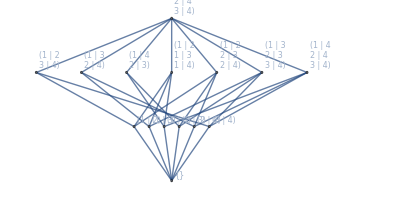

<|{}→{{}},{{1,2}}→{{{1,2}}},{{1,3}}→{{{1,3}}},{{1,4}}→{{{1,4}}},{{2,3}}→{{{2,3}}},{{2,4}}→{{{2,4}}},{{3,4}}→{{{3,4}}},{{1,2},{3,4}}→{{{1,2},{3,4}}},{{1,3},{2,4}}→{{{1,3},{2,4}}},{{1,4},{2,3}}→{{{1,4},{2,3}}},{{1,2},{1,3},{1,4}}→{{{1,2},{1,3}},{{1,2},{1,4}},{{1,3},{1,4}},{{1,2},{1,3},{1,4}}},{{1,2},{2,3},{2,4}}→{{{1,2},{2,3}},{{1,2},{2,4}},{{2,3},{2,4}},{{1,2},{2,3},{2,4}}},{{1,3},{2,3},{3,4}}→{{{1,3},{2,3}},{{1,3},{3,4}},{{2,3},{3,4}},{{1,3},{2,3},{3,4}}},{{1,4},{2,4},{3,4}}→{{{1,4},{2,4}},{{1,4},{3,4}},{{2,4},{3,4}},{{1,4},{2,4},{3,4}}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}→{{{1,2},{1,3},{2,3}},{{1,2},{1,3},{2,4}},{{1,2},{1,3},{3,4}},{{1,2},{1,4},{2,3}},{{1,2},{1,4},{2,4}},{{1,2},{1,4},{3,4}},{{1,2},{2,3},{3,4}},{{1,2},{2,4},{3,4}},{{1,3},{1,4},{2,3}},{{1,3},{1,4},{2,4}},{{1,3},{1,4},{3,4}},{{1,3},{2,3},{2,4}},{{1,3},{2,4},{3,4}},{{1,4},{2,3},{2,4}},{{1,4},{2,3},{3,4}},{{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3}},{{1,2},{1,3},{1,4},{2,4}},{{1,2},{1,3},{1,4},{3,4}},{{1,2},{1,3},{2,3},{2,4}},{{1,2},{1,3},{2,3},{3,4}},{{1,2},{1,3},{2,4},{3,4}},{{1,2},{1,4},{2,3},{2,4}},{{1,2},{1,4},{2,3},{3,4}},{{1,2},{1,4},{2,4},{3,4}},{{1,2},{2,3},{2,4},{3,4}},{{1,3},{1,4},{2,3},{2,4}},{{1,3},{1,4},{2,3},{3,4}},{{1,3},{1,4},{2,4},{3,4}},{{1,3},{2,3},{2,4},{3,4}},{{1,4},{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{3,4}},{{1,2},{1,3},{1,4},{2,4},{3,4}},{{1,2},{1,3},{2,3},{2,4},{3,4}},{{1,2},{1,4},{2,3},{2,4},{3,4}},{{1,3},{1,4},{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}|>

```mathematica
M=UniformMatroid[3,4];
WedgeLattice[M,2]
```

```mathematica
FQ[Subsets[Range[4],{2}],Keys[%48]]
```

True

#### 2

Non uniform matroidal
n=5 d=3 k=2

7 bases

```mathematica
M=matroids[{5,3}][[4]]
```

{{1,2,3,4,5},{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{2,3,4},{2,3,5}}}

Note how the {4,5} circuit causes x_4+x_5 sim 0

```mathematica
Circuits[M]
```

{{4,5},{1,2,3,4},{1,2,3,5}}

Trivial and bend 0.

Remaining set 16.301407

Ground set size 10

Number of subsets 1024

Number of pairs 523776

Iterations needed 533047

Avg time per iteration 0.0000306

Loops done 1.0177

Changes done each loop {968,0}

Last change index 9271

Last change pair {{{3,5}},{{1,3},{2,3},{4,5}}}

Tree collapsed 0.5712158

Class size | # | Max elem. size | Min elem. size
2 | 4 | 2 | 0
6 | 6 | 4 | 1
20 | 3 | 5 | 2
108 | 1 | 7 | 2
812 | 1 | 10 | 3

Longest linear form length: 3

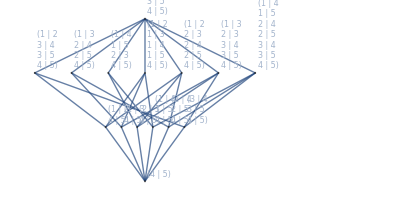

<|{{4,5}}→{{},{{4,5}}},13,{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}→{{{1,2},{1,3},{2,3}},{{1,2},{1,3},{2,4}},{{1,2},{1,3},{2,5}},{{1,2},{1,3},{3,4}},{{1,2},{1,3},{3,5}},{{1,2},{1,4},{2,3}},800,{{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}}|>
 |  |  |  |

```mathematica
WedgeLattice[M,2]
```

#### 3

6 bases

```mathematica
M=matroids[{5,3}][[5]]
```

{{1,2,3,4,5},{{1,2,4},{1,2,5},{1,3,4},{1,3,5},{2,3,4},{2,3,5}}}

```mathematica
Circuits[M]
```

{{4,5},{1,2,3}}

Trivial and bend 0.

Remaining set 16.516343

Ground set size 10

Number of subsets 1024

Number of pairs 523776

Iterations needed 532948

Avg time per iteration 0.000031

Loops done 1.01751

Changes done each loop {991,0}

Last change index 9172

Last change pair {{{3,5}},{{4,5}}}

Tree collapsed 0.5495925

Class size | # | Max elem. size | Min elem. size
2 | 1 | 1 | 0
6 | 3 | 3 | 1
14 | 1 | 4 | 1
42 | 3 | 6 | 2
108 | 1 | 7 | 2
756 | 1 | 10 | 3

Longest linear form length: 3

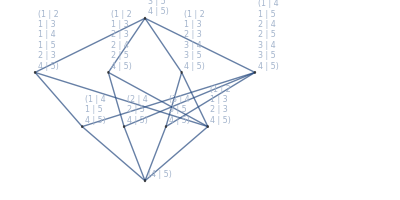

<|{{4,5}}→{{},{{4,5}}},8,{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}→{{{1,2},{1,4},{2,4}},{{1,2},{1,4},{2,5}},{{1,2},{1,4},{3,4}},{{1,2},{1,4},{3,5}},{{1,2},{1,5},{2,4}},{{1,2},{1,5},{2,5}},744,{{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}}|>
 |  |  |  |

```mathematica
WedgeLattice[M,2]
```

```mathematica
classes=%;
reps=Keys[classes]
```

{{{4,5}},{{1,4},{1,5},{4,5}},{{2,4},{2,5},{4,5}},{{3,4},{3,5},{4,5}},{{1,2},{1,3},{2,3},{4,5}},{{1,2},{1,3},{1,4},{1,5},{2,3},{4,5}},{{1,2},{1,3},{2,3},{2,4},{2,5},{4,5}},{{1,2},{1,3},{2,3},{3,4},{3,5},{4,5}},{{1,4},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}}

```mathematica
FQ[Subsets[Range[5],{2}],reps]
```

True

#### Compare lattices

Note how 2 and 3 have the same smallest flat. And presumably, having smaller circuits in 3 results in fewer flats than 2.

## 3/26

### Checking BendCongruencesNew

```mathematica
M=UniformMatroid[3,6];
k=2;
```

Trivial and bend 0.0813824

Remaining set 14.067413

Ground set size 15

Number of pairs checked 524047

Changes done 32534

Last change indices {16,5047}

Last change pair {{{5,6}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}

Avg iterations per second 37300.

Tree collapsed 0.5786141

Class size | # | Max elem. size | Min elem. size
1 | 76 | 3 | 0
26 | 6 | 5 | 2
32536 | 1 | 15 | 3

Longest linear form length: 3

Failed, for

{{1,2},{1,3},{1,4}}

{{1,2},{1,3},{2,3},{5,6}}

{1,2}

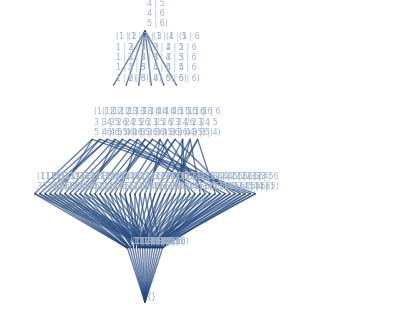

```mathematica
classes=WedgeLatticeNew[M,k];
```

```mathematica
f=SystemDialogInput["FileOpen"]
```

C:\Users\Nick\Documents\Undergrad\Labs\Marcus\Data\U(3,6)k=2.txt

```mathematica
computedClasses=ToExpression@Import[f];
```

```mathematica
classes==computedClasses
```

True

### 6,3,2

```mathematica
n=6;d=3;k=2;
Ms=matroids[{n,d}];
Length[Ms]
MatroidalQNew[#,k]&/@Ms
```

38

Failed F3 for

F {{1,2},{3,4}}

Union of F_i-F is not E-F

Failed F3 for

F {{1,4},{2,5}}

Union of F_i-F is not E-F

Failed F3 for

F {{1,4},{2,5}}

Union of F_i-F is not E-F

Failed F3 for

F {{1,6},{2,4}}

Union of F_i-F is not E-F

Failed F3 for

F {{1,6},{2,5}}

Union of F_i-F is not E-F

Failed F3 for

F {{1,6},{2,5}}

Union of F_i-F is not E-F

{False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

-Graphics-

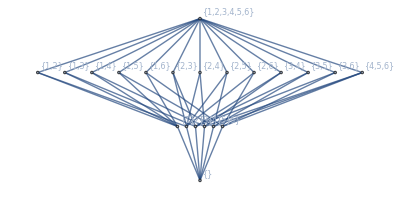

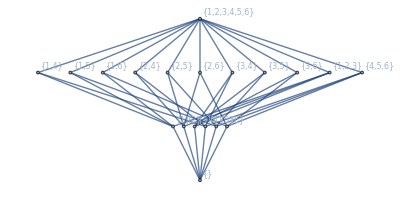

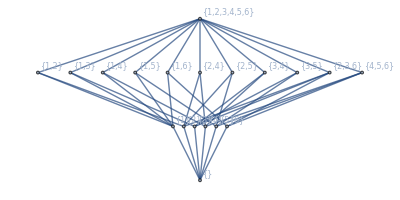

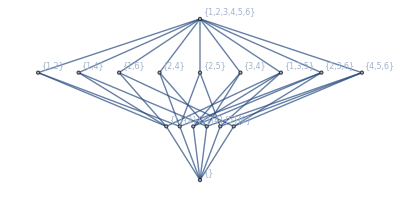

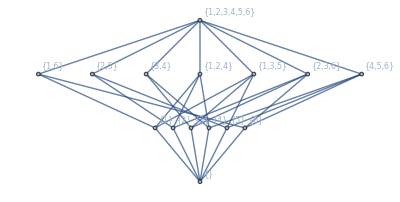

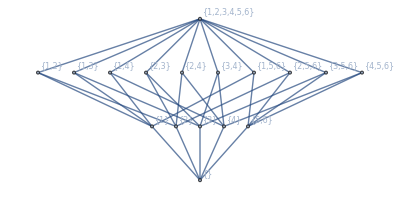

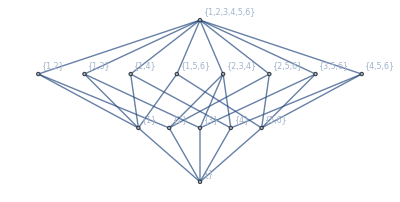

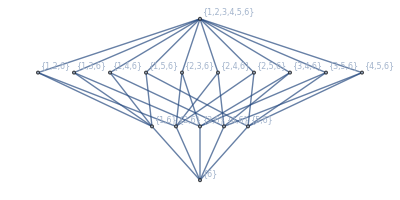

{<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{5}→{{5}},{6}→{{6}},9,{3,4}→{{3,4}},{3,5}→{{3,5}},{3,6}→{{3,6}},{4,5}→{{4,5}},{4,6}→{{4,6}},{5,6}→{{5,6}},{1,2,3,4,5,6}→{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6},{1,2,5,6},{1,3,4,5},{1,3,4,6},{1,3,5,6},{1,4,5,6},{2,3,4,5},{2,3,4,6},{2,3,5,6},{2,4,5,6},{3,4,5,6},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6},{1,2,3,4,5,6}}|>,36,<|1|>}
 |  |  |  |

```mathematica
LatticeOfFlats/@Ms
```

### 6,5,2

#### 1

```mathematica
n=7;d=3;k=2;
Ms=matroids[{n,d}];
Length[Ms]
```

108

```mathematica
M=Ms[[1]]
```

{{1,2,3,4,5,6,7},{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,5,7},{1,6,7},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,6},{2,4,7},{2,5,6},{2,5,7},{2,6,7},{3,4,5},{3,4,6},{3,4,7},{3,5,6},{3,5,7},{3,6,7},{4,5,6},{4,5,7},{4,6,7},{5,6,7}}}

```mathematica
MatroidalQNew[M,k]
```

Failed F3 for

F {{1,2},{3,4}}

Union of F_i-F is not E-F

False

#### 2

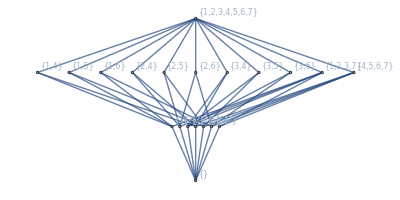

```mathematica
M=Ms[[24]];
LatticeOfFlats[M];
```

```mathematica
MatroidalQNew[M,k]
```

Failed F3 for

F {{1,4},{2,5}}

Union of F_i-F is not E-F

False

#### 3

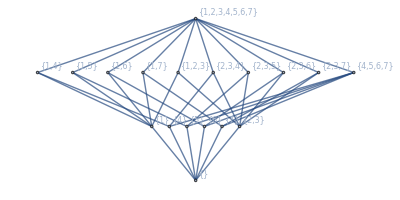

```mathematica
M=Ms[[25]];
LatticeOfFlats[M];
```

```mathematica
MatroidalQNew[M,k]
```

True

#### 4

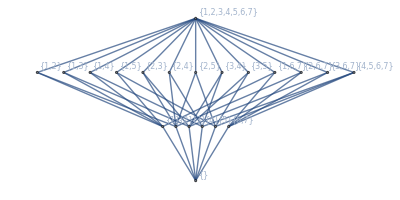

```mathematica
M=Ms[[26]];
LatticeOfFlats[M];
```

```mathematica
MatroidalQNew[M,k]
```

Failed F3 for

F {{1,4},{2,5},{6,7}}

Union of F_i-F is not E-F

False